```mathematica
showDs[positions_]:=Module[{lst1,lst2,lst3,pos1,pos2,pos3,mk1,mk2,mk3,plt1,plt2,plt3},

{pos1,pos2}=positions;
pos3=Complement[Table[i,{i,1,5}],pos1,pos2];

lst1=Joinlists[pos1,Table[0,{i,1,Length[pos1]}]];
lst2=Joinlists[pos2,Table[0,{i,1,Length[pos2]}]];
lst3=Joinlists[pos3,Table[0,{i,1,Length[pos3]}]];

mk1=Graphics[{Black,Disk[]}];
mk2=Graphics[{Black,Thick,Circle[]}];
mk3=Graphics[{Green,Rectangle[]}];

plt1=ListPlot[lst1,PlotRange->{{0.8,5.2},{-0.2,+0.2}},PlotMarkers->{mk1,0.1},Axes->{True,False},ImageSize->Large];
plt2=ListPlot[lst2,PlotRange->{{0.8,5.2},{-0.2,+0.2}},PlotMarkers->{mk2,0.1},Axes->{True,False},ImageSize->Large];
plt3=ListPlot[lst3,PlotRange->{{0.8,5.2},{-0.2,+0.2}},PlotMarkers->{mk3,0.1},Axes->{True,False},ImageSize->Large];
Show[plt1,plt2,plt3]
];
```

```mathematica
mtot=mvst+Length/@Dsvst;
nt=20;
x=showDs/@DPhis[[1;;nt]];

Manipulate[
Column[{x[[i]],
Grid[{{"m = ",mvst[[i]]},{"m+N_d = ",mtot[[i]]}}]},Alignment->Left],{i,1,nt,1},ContentSize->{600, 460}]
```

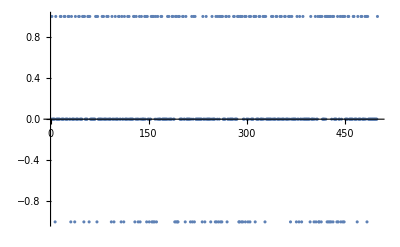

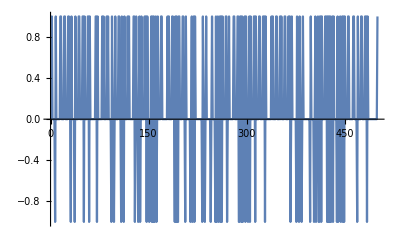

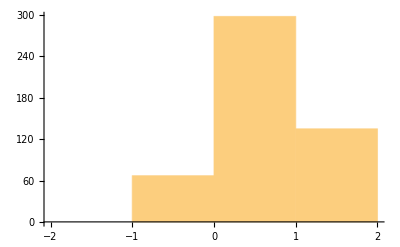

```mathematica
x=out[[1]][[;;,3]];
ListPlot[x]
ListLinePlot[x]
Histogram[x]
```

```mathematica
Mean[x]//N
```

0.136

```mathematica
ListPlot[x]
```

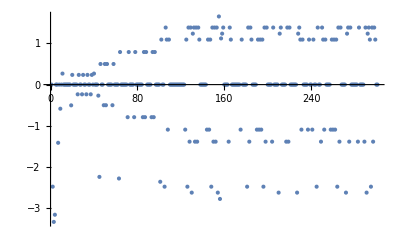

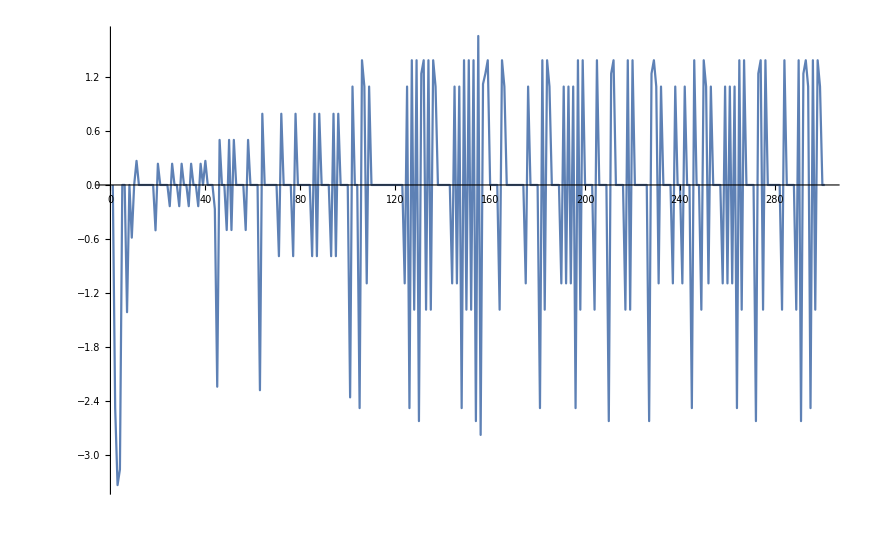

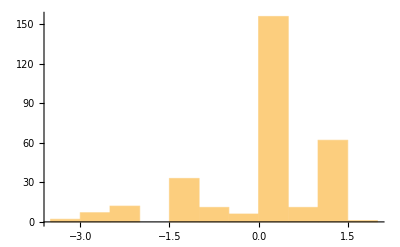

```mathematica
ListPlot[out[[2]]]
ListLinePlot[out[[2]]]
Histogram[out[[2]]]
```

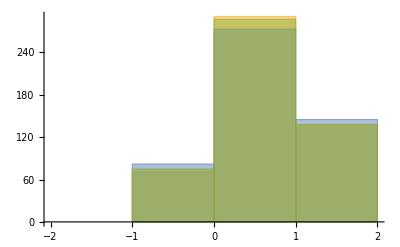

0.134

0.126

0.126

0.134

```mathematica
x1=out1[[1]][[;;,3]];(*g= 0.25, 1,5,10,50*)
x2=out2[[1]][[;;,3]];
x3=out3[[1]][[;;,3]];
x4=out4[[1]][[;;,3]];


Histogram[{x1,x2,x3}]
mx1=Mean[x1]//N
mx2=Mean[x2]//N
mx3=Mean[x3]//N
mx4=Mean[x4]//N
```